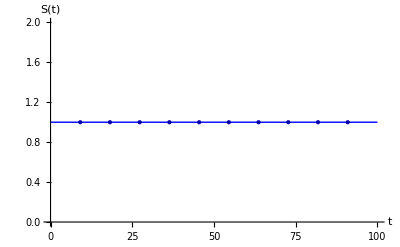

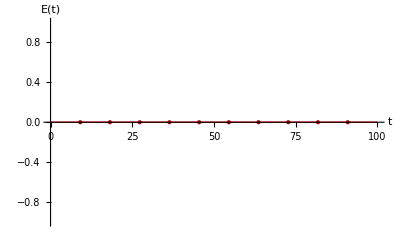

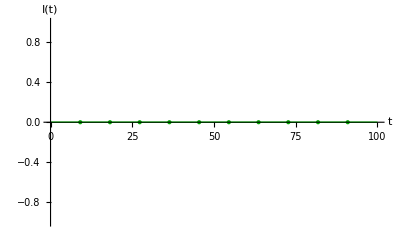

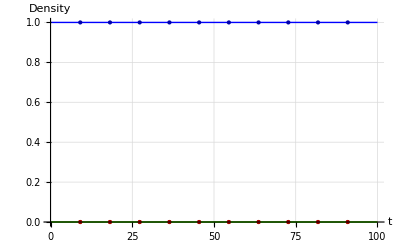

```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=-β * s[t]* i[t]/n;
eq2=β*s[t]*i[t]/n-ϵ*e[t];
eq3=ϵ*e[t];
n=1;
β=0.8;
ϵ=0.5;
tf=100;
szero=1.0;
ezero=0.0;
izero=0.0;
R0*szero;

sol=NDSolve[{s'[t]==eq1,e'[t]==eq2,i'[t]==eq3,s[0]==szero,e[0]==ezero,i[0]==izero},{s,e,i},{t,tf}];

plot1=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"S"[t]},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue]      (* For S[t] versus t *)
plot1a=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]; (* For S[t] versus t *)


plot2=Plot[b[t]=Evaluate[e[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"E"[t]},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red]    (* For E[t] versus t *)
plot2a=Plot[b[t]=Evaluate[e[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Orange,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]] ;


plot3=Plot[c[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"I"[t]},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green]    (* For I[t] versus t *)
plot3a=Plot[c[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]];


ShowLegend[Show[plot1a ,plot2a,plot3a],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],"S(t)"},{Graphics[{Orange,Line[{{0,0},{1,0}}]}],"E(t)"},{Graphics[{Red,Line[{{0,0},{1,0}}]}],"I(t)"}},LegendShadow->None,LegendSpacing->0,LegendSize-> {0.5,0.5}}]

plotall=Plot[{Evaluate[s[t]/.sol],Evaluate[e[t]/.sol],Evaluate[i[t]/.sol]},{t,0,tf},PlotRange->{{0,tf},{-0.05,1.1}},PlotLegend->{"S(t)","E(t)","I(t)"}, PlotStyle->{{Thick,Blue},{Thick,Orange},{Thick,Red}},LegendShadow->None,LegendSpacing->0,LegendPosition->{0.2,0},LegendSize-> {0.2,0.3},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Density ",""},{"time "[t],""}}]

(*plotP=ParametricPlot[Evaluate[{x1[t],x2[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"E"[t]}]
plotQ=ParametricPlot[Evaluate[{x2[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{"E"[t],"I"[t]}]
plotR=ParametricPlot[Evaluate[{x1[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"I"[t]}]
h1[t_]:=Evaluate[x1[t]/.sol]
h2[t_]:=Evaluate[x2[t]/.sol]
h3[t_]:=Evaluate[x3[t]/.sol]*)
```

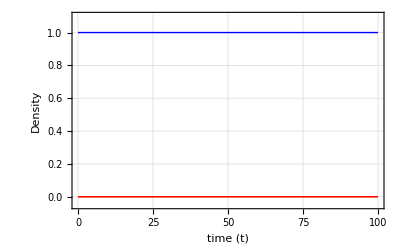

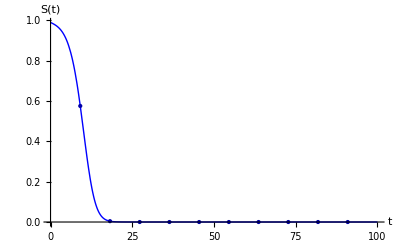

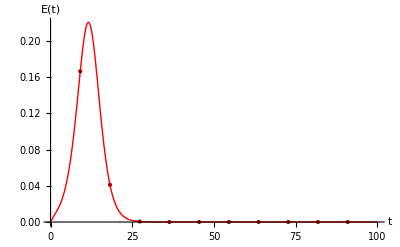

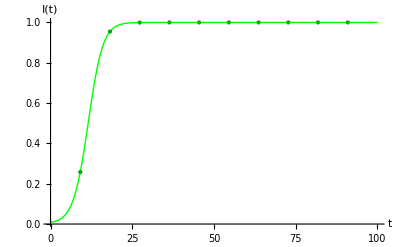

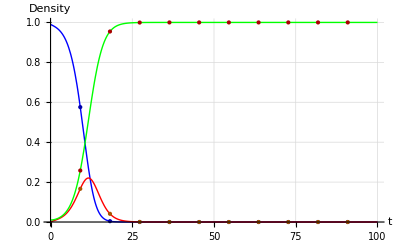

```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=-β * s[t]* i[t]/n;
eq2=β*s[t]*i[t]/n-ϵ*e[t];
eq3=ϵ*e[t];
n=1;
β=0.8;
ϵ=0.5;
R0=N[β/ϵ];
tf=100;
szero=0.99;
ezero=0.0;
izero=0.01;

sol=NDSolve[{s'[t]==eq1,e'[t]==eq2,i'[t]==eq3,s[0]==szero,e[0]==ezero,i[0]==izero},{s,e,i},{t,tf}];

plot1=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"S"[t]},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue]      (* For S[t] versus t *)
plot1a=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]; (* For S[t] versus t *)


plot2=Plot[b[t]=Evaluate[e[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"E"[t]},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red]    (* For E[t] versus t *)
plot2a=Plot[b[t]=Evaluate[e[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Orange,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]] ;


plot3=Plot[c[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"I"[t]},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green]    (* For I[t] versus t *)
plot3a=Plot[c[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]];


ShowLegend[Show[plot1a ,plot2a,plot3a],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],"S(t)"},{Graphics[{Orange,Line[{{0,0},{1,0}}]}],"E(t)"},{Graphics[{Red,Line[{{0,0},{1,0}}]}],"I(t)"}},LegendShadow->None,LegendSpacing->0,LegendSize-> {0.5,0.5}}]

plotall=Plot[{Evaluate[s[t]/.sol],Evaluate[e[t]/.sol],Evaluate[i[t]/.sol]},{t,0,tf},PlotRange->{{0,tf},{-0.05,1.1}},PlotLegend->{"S(t)","E(t)","I(t)"}, PlotStyle->{{Thick,Blue},{Thick,Orange},{Thick,Red}},LegendShadow->None,LegendSpacing->0,LegendPosition->{0.2,0},LegendSize-> {0.2,0.3},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Density ",""},{"time "[t],""}}]

(*plotP=ParametricPlot[Evaluate[{x1[t],x2[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"E"[t]}]
plotQ=ParametricPlot[Evaluate[{x2[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{"E"[t],"I"[t]}]
plotR=ParametricPlot[Evaluate[{x1[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"I"[t]}]
h1[t_]:=Evaluate[x1[t]/.sol]
h2[t_]:=Evaluate[x2[t]/.sol]
h3[t_]:=Evaluate[x3[t]/.sol]*)
```

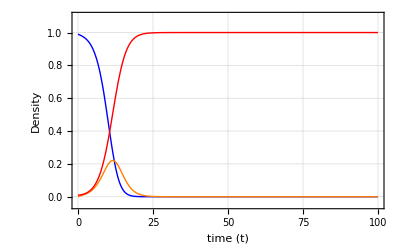

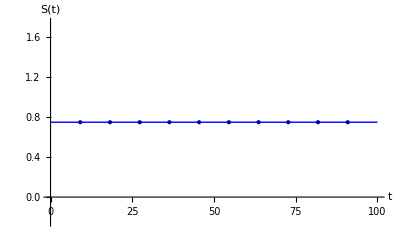

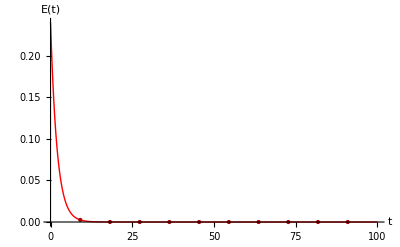

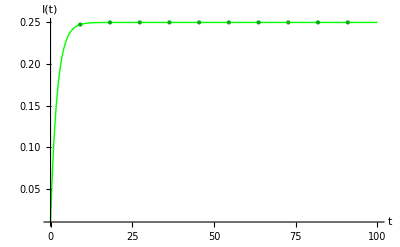

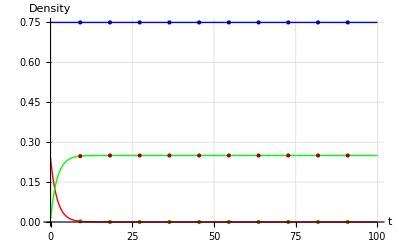

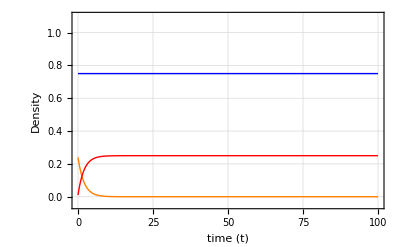

```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=-β * s[t]* i[t]/n;
eq2=β*s[t]*i[t]/n-ϵ*e[t];
eq3=ϵ*e[t];
n=1;
β=0.0;
ϵ=0.5;
R0=N[β/ϵ];
tf=100;
szero=0.75;
ezero=0.24;
izero=0.01;

sol=NDSolve[{s'[t]==eq1,e'[t]==eq2,i'[t]==eq3,s[0]==szero,e[0]==ezero,i[0]==izero},{s,e,i},{t,tf}];

plot1=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"S"[t]},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue]      (* For S[t] versus t *)
plot1a=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]; (* For S[t] versus t *)


plot2=Plot[b[t]=Evaluate[e[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"E"[t]},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red]    (* For E[t] versus t *)
plot2a=Plot[b[t]=Evaluate[e[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Orange,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]] ;


plot3=Plot[c[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"I"[t]},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green]    (* For I[t] versus t *)
plot3a=Plot[c[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]];


ShowLegend[Show[plot1a ,plot2a,plot3a],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],"S(t)"},{Graphics[{Orange,Line[{{0,0},{1,0}}]}],"E(t)"},{Graphics[{Red,Line[{{0,0},{1,0}}]}],"I(t)"}},LegendShadow->None,LegendSpacing->0,LegendSize-> {0.5,0.5}}]

plotall=Plot[{Evaluate[s[t]/.sol],Evaluate[e[t]/.sol],Evaluate[i[t]/.sol]},{t,0,tf},PlotRange->{{0,tf},{-0.05,1.1}},PlotLegend->{"S(t)","E(t)","I(t)"}, PlotStyle->{{Thick,Blue},{Thick,Orange},{Thick,Red}},LegendShadow->None,LegendSpacing->0,LegendPosition->{0.2,0},LegendSize-> {0.2,0.3},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Density ",""},{"time "[t],""}}]

(*plotP=ParametricPlot[Evaluate[{x1[t],x2[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"E"[t]}]
plotQ=ParametricPlot[Evaluate[{x2[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{"E"[t],"I"[t]}]
plotR=ParametricPlot[Evaluate[{x1[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"I"[t]}]
h1[t_]:=Evaluate[x1[t]/.sol]
h2[t_]:=Evaluate[x2[t]/.sol]
h3[t_]:=Evaluate[x3[t]/.sol]*)
```

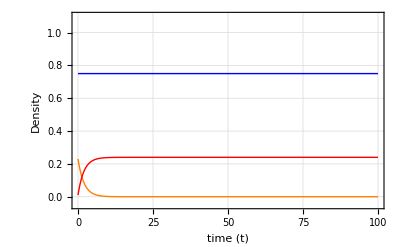

Power::infy: Infinite expression 1/0. encountered.

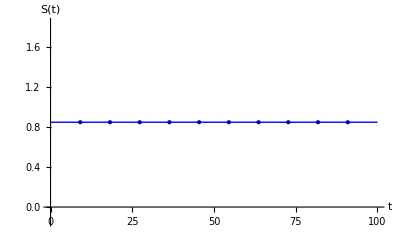

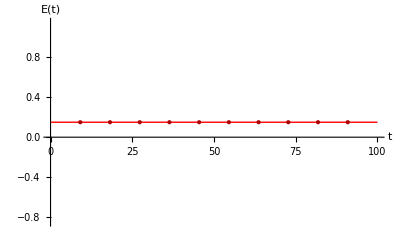

-Graphics-

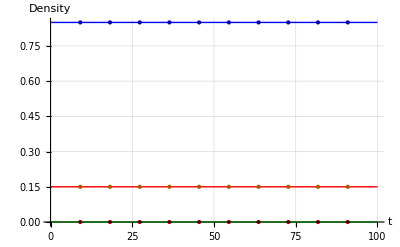

```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=-β * s[t]* i[t]/n;
eq2=β*s[t]*i[t]/n-ϵ*e[t];
eq3=ϵ*e[t];
n=1;
β=0.8;
ϵ=0.0;
R0=N[β/ϵ];
tf=100;
szero=0.85;
ezero=0.15;
izero=0.0;

sol=NDSolve[{s'[t]==eq1,e'[t]==eq2,i'[t]==eq3,s[0]==szero,e[0]==ezero,i[0]==izero},{s,e,i},{t,tf}];

plot1=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"S"[t]},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue]      (* For S[t] versus t *)
plot1a=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]; (* For S[t] versus t *)


plot2=Plot[b[t]=Evaluate[e[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"E"[t]},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red]    (* For E[t] versus t *)
plot2a=Plot[b[t]=Evaluate[e[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Orange,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]] ;


plot3=Plot[c[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"I"[t]},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green]    (* For I[t] versus t *)
plot3a=Plot[c[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]];


ShowLegend[Show[plot1a ,plot2a,plot3a],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],"S(t)"},{Graphics[{Orange,Line[{{0,0},{1,0}}]}],"E(t)"},{Graphics[{Red,Line[{{0,0},{1,0}}]}],"I(t)"}},LegendShadow->None,LegendSpacing->0,LegendSize-> {0.5,0.5}}]

plotall=Plot[{Evaluate[s[t]/.sol],Evaluate[e[t]/.sol],Evaluate[i[t]/.sol]},{t,0,tf},PlotRange->{{0,tf},{-0.05,1.1}},PlotLegend->{"S(t)","E(t)","I(t)"}, PlotStyle->{{Thick,Blue},{Thick,Orange},{Thick,Red}},LegendShadow->None,LegendSpacing->0,LegendPosition->{0.2,0},LegendSize-> {0.2,0.3},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Density ",""},{"time "[t],""}}]

(*plotP=ParametricPlot[Evaluate[{x1[t],x2[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"E"[t]}]
plotQ=ParametricPlot[Evaluate[{x2[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{"E"[t],"I"[t]}]
plotR=ParametricPlot[Evaluate[{x1[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"I"[t]}]
h1[t_]:=Evaluate[x1[t]/.sol]
h2[t_]:=Evaluate[x2[t]/.sol]
h3[t_]:=Evaluate[x3[t]/.sol]*)
```

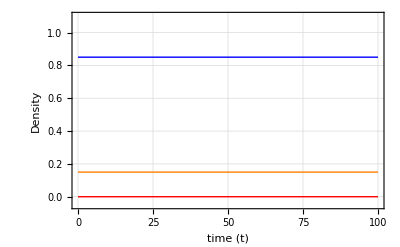

Power::infy: Infinite expression 1/0. encountered.

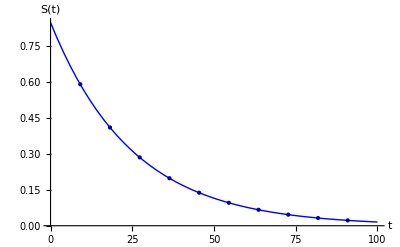

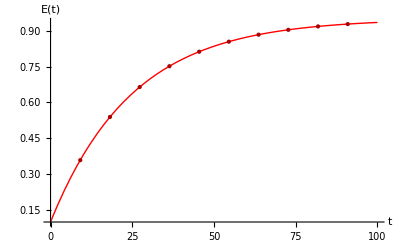

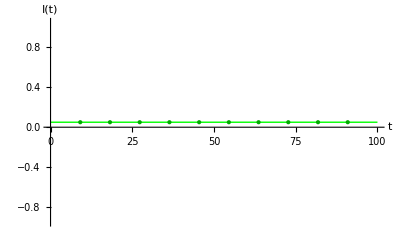

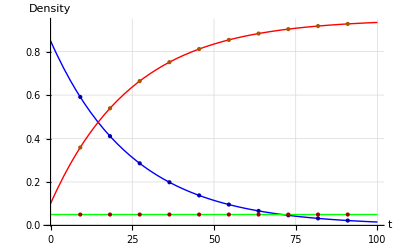

```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=-β * s[t]* i[t]/n;
eq2=β*s[t]*i[t]/n-ϵ*e[t];
eq3=ϵ*e[t];
n=1;
β=0.8;
ϵ=0.0;
R0=N[β/ϵ];
tf=100;
szero=0.85;
ezero=0.1;
izero=0.05;

sol=NDSolve[{s'[t]==eq1,e'[t]==eq2,i'[t]==eq3,s[0]==szero,e[0]==ezero,i[0]==izero},{s,e,i},{t,tf}];

plot1=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"S"[t]},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue]      (* For S[t] versus t *)
plot1a=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]; (* For S[t] versus t *)


plot2=Plot[b[t]=Evaluate[e[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"E"[t]},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red]    (* For E[t] versus t *)
plot2a=Plot[b[t]=Evaluate[e[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Orange,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]] ;


plot3=Plot[c[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"I"[t]},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green]    (* For I[t] versus t *)
plot3a=Plot[c[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]];


ShowLegend[Show[plot1a ,plot2a,plot3a],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],"S(t)"},{Graphics[{Orange,Line[{{0,0},{1,0}}]}],"E(t)"},{Graphics[{Red,Line[{{0,0},{1,0}}]}],"I(t)"}},LegendShadow->None,LegendSpacing->0,LegendSize-> {0.5,0.5}}]

plotall=Plot[{Evaluate[s[t]/.sol],Evaluate[e[t]/.sol],Evaluate[i[t]/.sol]},{t,0,tf},PlotRange->{{0,tf},{-0.05,1.1}},PlotLegend->{"S(t)","E(t)","I(t)"}, PlotStyle->{{Thick,Blue},{Thick,Orange},{Thick,Red}},LegendShadow->None,LegendSpacing->0,LegendPosition->{0.2,0},LegendSize-> {0.2,0.3},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Density ",""},{"time "[t],""}}]

(*plotP=ParametricPlot[Evaluate[{x1[t],x2[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"E"[t]}]
plotQ=ParametricPlot[Evaluate[{x2[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{"E"[t],"I"[t]}]
plotR=ParametricPlot[Evaluate[{x1[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"I"[t]}]
h1[t_]:=Evaluate[x1[t]/.sol]
h2[t_]:=Evaluate[x2[t]/.sol]
h3[t_]:=Evaluate[x3[t]/.sol]*)
```

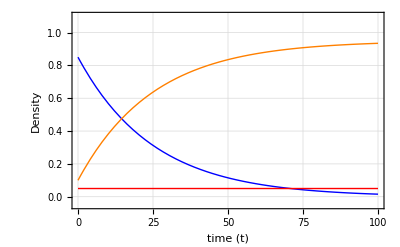

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

-Graphics-

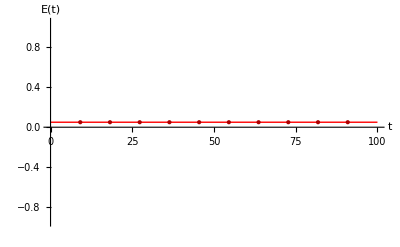

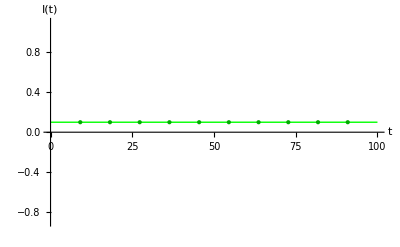

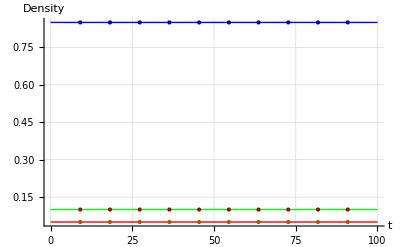

```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=-β * s[t]* i[t]/n;
eq2=β*s[t]*i[t]/n-ϵ*e[t];
eq3=ϵ*e[t];
n=1;
β=0.0;
ϵ=0.0;
R0=N[β/ϵ];
tf=100;
szero=0.85;
ezero=0.05;
izero=0.1;

sol=NDSolve[{s'[t]==eq1,e'[t]==eq2,i'[t]==eq3,s[0]==szero,e[0]==ezero,i[0]==izero},{s,e,i},{t,tf}];

plot1=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"S"[t]},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue]      (* For S[t] versus t *)
plot1a=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]; (* For S[t] versus t *)


plot2=Plot[b[t]=Evaluate[e[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"E"[t]},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red]    (* For E[t] versus t *)
plot2a=Plot[b[t]=Evaluate[e[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Orange,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]] ;


plot3=Plot[c[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"I"[t]},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green]    (* For I[t] versus t *)
plot3a=Plot[c[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]];


ShowLegend[Show[plot1a ,plot2a,plot3a],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],"S(t)"},{Graphics[{Orange,Line[{{0,0},{1,0}}]}],"E(t)"},{Graphics[{Red,Line[{{0,0},{1,0}}]}],"I(t)"}},LegendShadow->None,LegendSpacing->0,LegendSize-> {0.5,0.5}}]

plotall=Plot[{Evaluate[s[t]/.sol],Evaluate[e[t]/.sol],Evaluate[i[t]/.sol]},{t,0,tf},PlotRange->{{0,tf},{-0.05,1.1}},PlotLegend->{"S(t)","E(t)","I(t)"}, PlotStyle->{{Thick,Blue},{Thick,Orange},{Thick,Red}},LegendShadow->None,LegendSpacing->0,LegendPosition->{0.2,0},LegendSize-> {0.2,0.3},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Density ",""},{"time "[t],""}}]

(*plotP=ParametricPlot[Evaluate[{x1[t],x2[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"E"[t]}]
plotQ=ParametricPlot[Evaluate[{x2[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{"E"[t],"I"[t]}]
plotR=ParametricPlot[Evaluate[{x1[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"I"[t]}]
h1[t_]:=Evaluate[x1[t]/.sol]
h2[t_]:=Evaluate[x2[t]/.sol]
h3[t_]:=Evaluate[x3[t]/.sol]*)
```